```mathematica
SetDirectory[NotebookDirectory[]];
<<CIP`CurveFit`
```

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

# V7 - Auswertung

### Import aller Messdaten

```mathematica
rawData=Import["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v7\\v7_messdaten.csv"]
trawData=Import["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v7\\Adsorption.csv"]
```

{{c0,V,VHAc},{0.8,19.1,2.5},{0.8,21.6,2.5},{0.8,20.6,2.5},{0.5,18.5,4},{0.5,19.1,4},{0.5,18.2,4},{0.3,13.3,6},{0.3,12.8,6},{0.3,13.,6},{0.2,24.9,10},{0.2,24.,10},{0.2,23.,10},{0.1,29.6,20},{0.1,29.,20},{0.1,29.6,20},{0.05,5.3,20},{0.05,5.1,20},{0.05,5.1,20}}

{{Konz [mol / l],V Titriert [ml],V Vorgelegt [ml],A Kohle [g]},{0.8,16.2,3,1.0025},{0.8,16.,3,1.0025},{0.8,16.4,3,1.0025},{0.5,13.6,4,1.0021},{0.5,13.8,4,1.0021},{0.5,13.4,4,1.0021},{0.3,13,7,1.003},{0.3,13,9,1.003},{0.3,13,5,1.003},{0.2,12.1,10,1.0021},{0.2,12.3,10,1.0021},{0.2,12.,10,1.0021},{0.1,11.1,20,1.0007},{0.1,11.3,20,1.0007},{0.1,11.,20,1.0007},{0.05,9.,40,1.0001},{0.05,9.2,40,1.0001},{0.05,9.4,40,1.0001}}

```mathematica
rawDataT=Transpose[Drop[rawData,1]]
```

{{0.8,0.8,0.8,0.5,0.5,0.5,0.3,0.3,0.3,0.2,0.2,0.2,0.1,0.1,0.1,0.05,0.05,0.05},{19.1,21.6,20.6,18.5,19.1,18.2,13.3,12.8,13.,24.9,24.,23.,29.6,29.,29.6,5.3,5.1,5.1},{2.5,2.5,2.5,4,4,4,6,6,6,10,10,10,20,20,20,20,20,20}}

### Bestimmung der Gleichgewichtskonzentration

```mathematica
cg[c_,V_]:=c/V
```

```mathematica
cgRawData=Map[cg[0.1,#]&,rawDataT[[2]]]
cgMeanData=Map[Mean[#]&,Partition[cgRawData,3]];
cgSdData=Map[StandardDeviation[#]&,Partition[cgRawData,3]];
uncertainCgMeanData=Flatten[Transpose[{Around@@@Transpose[{cgMeanData,cgSdData}]}]]
```

{0.0052356,0.00462963,0.00485437,0.00540541,0.0052356,0.00549451,0.0075188,0.0078125,0.00769231,0.00401606,0.00416667,0.00434783,0.00337838,0.00344828,0.00337838,0.0188679,0.0196078,0.0196078}

{0.004910.00031,0.005380.00013,0.007670.00015,0.004180.00017,0.003400.00004,0.01940.0004}

```mathematica
cgDataLangmuir=1/uncertainCgMeanData
cgDataFreundlich=Log10[uncertainCgMeanData]
```

{204.13.,186.5.,130.32.5,239.10.,294.03.5,51.61.1}

{-2.3090.027,-2.2690.011,-2.1150.008,-2.3790.017,-2.4680.005,-1.7130.010}

### Bestimmung der Adsorptionsmolalität

```mathematica
mAd[c0_,cg_,VHAc_]:=(c0-cg)/VHAc
```

```mathematica
mAdData={};
For[i=2,i<=Length[rawData],i++,
AppendTo[
mAdData,
mAd[rawData[[i,1]],cgRawData[[i-1]],rawData[[i,3]]]
];
];
mAdMeanData=Map[Mean[#]&,Partition[mAdData,3]];
mAdSdData=Map[StandardDeviation[#]&,Partition[mAdData,3]];
uncertainmAdSdData=Flatten[Transpose[{Around@@@Transpose[{mAdMeanData,mAdSdData}]}]]

mAdDataLangmuir=1/uncertainmAdSdData
mAdDataFreundlich=Log10[uncertainmAdSdData]
```

{0.318040.00012,0.1236550.000033,0.0487210.000025,0.0195820.000017,0.004829920,0.0015320.000021}

{3.14430.0012,8.08700.0022,20.5250.010,51.070.04,207.040.09,653.9.}

{-0.497520.00017,-0.907790.00012,-1.312280.00022,-1.70810.0004,-2.316060.00018,-2.8150.006}

### X, Y - Liste

#### Berechnung der Mittelwerte

```mathematica
cgMeanDataLangmuir=Map[Mean[#]&,Partition[cgDataLangmuir,3]];
cgMeanDataFreundlich=Map[Mean[#]&,Partition[cgDataFreundlich,3]];
mAdMeanDataLangmuir=Map[Mean[#]&,Partition[mAdDataLangmuir,3]];
mAdMeanDataFreundlich=Map[Mean[#]&,Partition[mAdDataFreundlich,3]];
```

#### Berechnung der Standardabweichungen

```mathematica
cgSdDataLangmuir=Map[StandardDeviation[#]&,Partition[cgDataLangmuir,3]];
cgSdDataFreundlich=Map[StandardDeviation[#]&,Partition[cgDataFreundlich,3]];
mAdSdDataLangmuir=Map[StandardDeviation[#]&,Partition[mAdDataLangmuir,3]];
mAdSdDataFreundlich=Map[StandardDeviation[#]&,Partition[mAdDataFreundlich,3]];
```

### CIP Integration für Langmuir-Modell

```mathematica
cgDataLangmuirX=cgDataLangmuir[[All,1]]
mAdDataLangmuirY=mAdDataLangmuir[[All,1]]
mAdDataLangmuirError=mAdDataLangmuir[[All,2]]
```

{203.81,185.925,130.301,239.415,293.973,51.6497}

{3.14428,8.08699,20.5251,51.0665,207.043,652.767}

{0.00121144,0.00215052,0.0103674,0.0433193,0.0864951,9.10144}

```mathematica
xyErrorTriple1L={cgDataLangmuirX[[1]],mAdDataLangmuirY[[1]],mAdDataLangmuirError[[1]]};
xyErrorTriple2L={cgDataLangmuirX[[2]],mAdDataLangmuirY[[2]],mAdDataLangmuirError[[2]]};
xyErrorTriple3L={cgDataLangmuirX[[3]],mAdDataLangmuirY[[3]],mAdDataLangmuirError[[3]]};
xyErrorTriple4L={cgDataLangmuirX[[4]],mAdDataLangmuirY[[4]],mAdDataLangmuirError[[4]]};
xyErrorTriple5L={cgDataLangmuirX[[5]],mAdDataLangmuirY[[5]],mAdDataLangmuirError[[5]]};
xyErrorTriple6L={cgDataLangmuirX[[6]],mAdDataLangmuirY[[6]],mAdDataLangmuirError[[6]]};
xyErrorTripleDataL={xyErrorTriple1L,xyErrorTriple2L,xyErrorTriple3L,xyErrorTriple4L,xyErrorTriple5L,xyErrorTriple6L};
```

{{203.81,3.14428,0.00121144},{185.925,8.08699,0.00215052},{130.301,20.5251,0.0103674}}

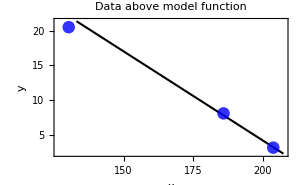

55.5921-0.257008 x

| Value | Standard error | Confidence region
Parameter | a→-2.57008×10^-1 | 1.01745×10^-4 | {-2.57195×10^-1,-2.56821×10^-1}
Parameter | b→5.55921×10^1 | 2.02534×10^-2 | {5.55549×10^1,5.56294×10^1}

Root mean squared error (RMSE) = 9.264×10^-1

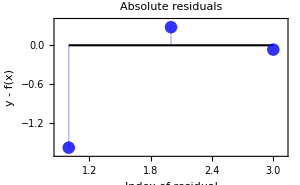

Standard deviation of fit = 3.776×10^-1

Out 1 : Correlation coefficient = 0.999026

```mathematica
xyErrorTripleDataL={xyErrorTriple1L,xyErrorTriple2L,xyErrorTriple3L}
modelFunction=a x+b;
argumentOfModelFunction=x;
parametersOfModelFunction={a,b};
curveFitInfoModel=CIP`CurveFit`FitModelFunction[
xyErrorTripleDataL,
modelFunction,
argumentOfModelFunction,
parametersOfModelFunction];
CIP`CurveFit`ShowFitResult[
{"FunctionPlot","ModelFunction","ParameterErrors","RMSE"},
xyErrorTripleDataL,
curveFitInfoModel]
CIP`CurveFit`ShowFitResult[
{"AbsoluteResidualsPlot","SDFit","CorrelationCoefficient"},
xyErrorTripleDataL,
curveFitInfoModel]
```

```mathematica
parameterALangmuir=Around[-0.257008224802933,"1.01745"×10^("-4")]
parameterBLangmuir=Around[55.592138449837044,"2.02534"×10^("-2")]
```

-0.257010.00010

55.5920.020

```mathematica
mAdMax=1/parameterBLangmuir
bLangmuir=1/(parameterALangmuir*mAdMax)
```

0.0179887

-216.300.12

m_ad_max = 0,0179882 +- 0,00000008
b = -216.30 +-0.12
R^2 = 0,999223
“Ausreißer” : 0.05; 0,1; 0,2

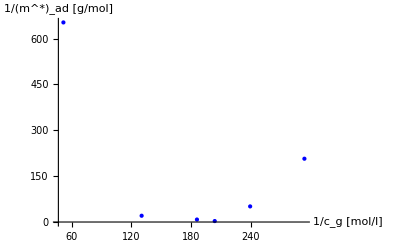

```mathematica
ListPlot[
Transpose[{cgDataLangmuirX,mAdDataLangmuirY}],
AxesLabel->{"1/c_g [mol/l]","1/(m^*)_ad [g/mol]"},
PlotStyle->{PointSize[Large],Blue}
]
```

### CIP Integration für Freundlich - Modell

```mathematica
cgDataFreundlichX=cgDataFreundlich[[All,1]]
mAdDataFreundlichY=mAdDataFreundlich[[All,1]]
mAdDataFreundlichError=mAdDataFreundlich[[All,2]]
```

{-2.30923,-2.26934,-2.11495,-2.37915,-2.46831,-1.71307}

{-0.497522,-0.907787,-1.31228,-1.70814,-2.31606,-2.81476}

{0.000167326,0.000115489,0.000219366,0.000368409,0.000181433,0.0060553}

```mathematica
xyErrorTriple1F={cgDataFreundlichX[[1]],mAdDataFreundlichY[[1]],mAdDataFreundlichError[[1]]};
xyErrorTriple2F={cgDataFreundlichX[[2]],mAdDataFreundlichY[[2]],mAdDataFreundlichError[[2]]};
xyErrorTriple3F={cgDataFreundlichX[[3]],mAdDataFreundlichY[[3]],mAdDataFreundlichError[[3]]};
xyErrorTriple4F={cgDataFreundlichX[[4]],mAdDataFreundlichY[[4]],mAdDataFreundlichError[[4]]};
xyErrorTriple5F={cgDataFreundlichX[[5]],mAdDataFreundlichY[[5]],mAdDataFreundlichError[[5]]};
xyErrorTriple6F={cgDataFreundlichX[[6]],mAdDataFreundlichY[[6]],mAdDataFreundlichError[[6]]};
xyErrorTripleDataF={xyErrorTriple1F,xyErrorTriple2F,xyErrorTriple3F,xyErrorTriple4F,xyErrorTriple5F,xyErrorTriple6F}
```

{{-2.30923,-0.497522,0.000167326},{-2.26934,-0.907787,0.000115489},{-2.11495,-1.31228,0.000219366},{-2.37915,-1.70814,0.000368409},{-2.46831,-2.31606,0.000181433},{-1.71307,-2.81476,0.0060553}}

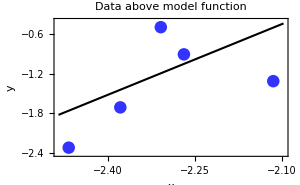

7.00462+3.55028 x

| Value | Standard error | Confidence region
Parameter | a→3.55028 | 7.68829×10^-4 | {3.54936,3.5512}
Parameter | b→7.00462 | 1.76944×10^-3 | {7.0025,7.00674}

Root mean squared error (RMSE) = 5.551×10^-1

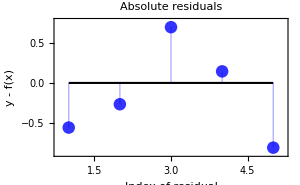

Standard deviation of fit = 6.463×10^-1

Out 1 : Correlation coefficient = 0.548248

```mathematica
xyErrorTripleDataF={xyErrorTriple1F,xyErrorTriple2F,xyErrorTriple3F,xyErrorTriple4F,xyErrorTriple5F};
modelFunction=a x+b;
argumentOfModelFunction=x;
parametersOfModelFunction={a,b};
curveFitInfoModel=CIP`CurveFit`FitModelFunction[
xyErrorTripleDataF,
modelFunction,
argumentOfModelFunction,
parametersOfModelFunction];
CIP`CurveFit`ShowFitResult[
{"FunctionPlot","ModelFunction","ParameterErrors","RMSE"},
xyErrorTripleDataF,
curveFitInfoModel]
CIP`CurveFit`ShowFitResult[
{"AbsoluteResidualsPlot","SDFit","CorrelationCoefficient"},
xyErrorTripleDataF,
curveFitInfoModel]
```

```mathematica
parameterBFreundlich=Around[7.004619896029063,0.000768829]
parameterAFreundlich=Around[3.55027952930021,0.00176944]
```

7.00460.0008

3.55030.0018

```mathematica
nF=1/parameterAFreundlich
KFPrime=10^parameterBFreundlich
```

0.281670.00014

1.01070.001810^7

n_F = 0.143146
K_F’ = 3482.24
R^2 = 0.547082
“Ausreißer” : 0.05

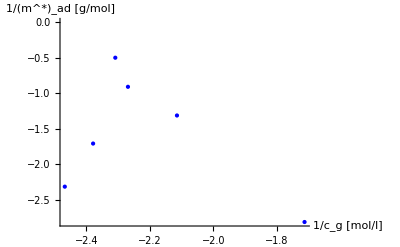

```mathematica
ListPlot[
Transpose[{cgDataFreundlichX,mAdDataFreundlichY}],
AxesLabel->{"1/c_g [mol/l]","1/(m^*)_ad [g/mol]"},
PlotStyle->{PointSize[Large],Blue}
]
```